```mathematica
(* this function generates a fib sequence using inflation rule *)
tau=(1+Sqrt[5])/2;
GenerateFibSequence[n_]:=Module[
{seq},
seq="A"; (* initial condition *)
Do[seq=StringReplace[seq,{"A"->"AB","B"->"A"}];,{i,n}];(* inflation rule for fib sequence *)
ToExpression[Characters[seq]]/.{A->1,B->tau}(* replace A, B with 1, tau *)
]
FibSeq=GenerateFibSequence[30];
```

```mathematica
ymin=-10;
ymax=10;
xmin=-10;
xmax=10;
numlines=80;
(*generate spacings for line*)
spacings=Module[
{seq},
cur=-numlines/2;
seq={cur};
Do[
cur+=N[FibSeq[[i]]];
seq=Append[seq,cur];,
{i,numlines}];
seq
];
```

```mathematica
a=2Pi/5;
r1={1,0,0};
r2={Cos[a],Sin[a],0};
r3={Cos[2a],Sin[2a],0};
r4={Cos[3a],Sin[3a],0};
r5={Cos[4a],Sin[4a],0};
starvectors={r1,r2,r3,r4};
numvectors=Length[starvectors];
startuples=Select[Tuples@{Range[numvectors],Range[numvectors]},Less@@#&];
starangles={a,2a,3a};(*excludes the first angle, which is zero, since this will be treated differently in plots*)
starslopes=Table[-1/Tan[x],{x,starangles[[{1,2,3}]]}];
basis =Graphics[Arrow[{{0,0},#}]&/@starvectors[[All,{1,2}]],Axes->True];
(*maxlength determines window size of n-grid, before mapping to tiles*)
(*essentially gives smallest inscribed square contained within all of the grids*)
maxlength=N[Min[Table[Abs[spacing/Sin[starangles[[i]]]/(1-starslopes[[i]])],{i,Range[numvectors-1]},{spacing,{spacings[[1]],spacings[[numlines+1]]}}]]];
```

```mathematica
(*this function finds intersection point of three grid lines, where e_i denotes star vector, and n_i denotes line number*)
FindIntersection[{n1_,e1_},{n2_,e2_},{n3_,e3_}]:=Module[
{p1,p2,p3,d},
p1=n1*e1;
p2=n2*e2;
p3=n3*e3;
d=N[Det[{e1,e2,e3}],{Infinity,150}];
If[d==0,{0,0,0},
Chop[N[1/d*
((p1.e1)Cross[e2,e3]+(p2.e2)Cross[e3,e1]+(p3.e3)Cross[e1,e2]),{Infinity,150}]]]
]
```

```mathematica
(*this function takes a point and finds the indices of the surrounding grid lines*)
FindGridIndices[x_]:=Table[Flatten[Position[spacings,_?(#>=x.y&)],1][[1]],{y,starvectors}]
```

```mathematica
(*this function returns the vertices and the tiles*)
FindQuasilattice[pt_]:=Module[
{m,n,i,j,x,MinIndex,MaxIndex,vertex,tile,pair,v},
m=pt[[1,1]];
n=pt[[1,2]];
i=pt[[2,1]];
j=pt[[2,2]];
x=pt[[3]];
vertex={};tile={};pair={};
If[Abs[x[[1]]]<maxlength &&Abs[x[[2]]]<maxlength,
If[VectorQ[N[FindGridIndices[x].starvectors],NumericQ],
Module[{},
vertex=N[FindGridIndices[x].starvectors];
v=Table[vertex+y,{y,{0,starvectors[[i]],starvectors[[j]],starvectors[[i]]+starvectors[[j]]}}][[All,{1,2}]];
tile=Graphics[Line[{
{v[[1]],v[[2]]},
{v[[2]],v[[4]]},
{v[[4]],v[[3]]},
{v[[3]],v[[1]]} }]];
pair={i,j};
]
]
];
{vertex,tile,pair}
]
```

```mathematica
(* ULTIMATE FUNCTION *)
(* finds intersections, with tuples of the form
{{m,n},{i,j},{x,y,z}} = {{indices of spacings},{indices of star vectors},{intersection point}} *)
pts=Table[
{{m,n},
{pair[[1]],pair[[2]]},
FindIntersection[{spacings[[m]],starvectors[[pair[[1]]]]},{spacings[[n]],starvectors[[pair[[2]]]]},{0,{0,0,1}}]
},
{m,Range[numlines]},{n,Range[numlines]},{pair,startuples}];
pts=Flatten[pts,2];
```

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating (-1/4 - √5/4)\ (-5/2\ (-1 - Power[« 2 »])^2 - 40\ (5/8 - √5/8)) + (1/4 + √5/4)\ (-5/2\ (-1 - Power[« 2 »])^2 - 40\ (5/8 - √5/8)).

```mathematica
Show[basis,
(*plots n-grid*)
Table[Plot[starslopes[[i]]*x+spacings[[j]]/Sin[starangles[[i]]],{x,-30,30},PlotStyle->{Blue,Thin}],{i,1,3},{j,Range[numlines]}],
Table[Graphics[{Blue,Thin,Line[{{spacings[[i]],-30},{spacings[[i]],30}}]}],{i,Range[numlines]}],

(*plots points*)
Graphics[{PointSize[0.005],Point[Cases[pts[[All,3]],{_?NumericQ,_?NumericQ,0}][[All,{1,2}]]]}],(*option here gets rid of indeterminate values*)

(*plots window*)
Graphics[{Red,Opacity[0.2],Polygon[{{-maxlength,-maxlength},{-maxlength,maxlength},{maxlength,maxlength},{maxlength,-maxlength},{-maxlength,-maxlength}}]}],

AspectRatio->1,PlotRange->{{-1.25maxlength,1.25maxlength},{-1.25maxlength,1.25maxlength}}]
```

```mathematica
(*From intersections, finds corresponding tiles and their vertices*)
tiles=Select[Table[FindQuasilattice[pt],{pt,pts}],UnsameQ[#,{{},{},{}}]&];
```

```mathematica
(*count number of tiles with starvectors (i,j)*)
Module[
{i,j},
Do[
i=n[[1]]; j=n[[2]];
Print["# tiles with starvectors (", i , ", ", j,"): ",Count[tiles[[All,3]],{i,j}]];
,{n,startuples}
]
]
```

# tiles with starvectors (1, 2): 2028

# tiles with starvectors (1, 3): 1254

# tiles with starvectors (1, 4): 1254

# tiles with starvectors (2, 3): 2038

# tiles with starvectors (2, 4): 1260

# tiles with starvectors (3, 4): 2040

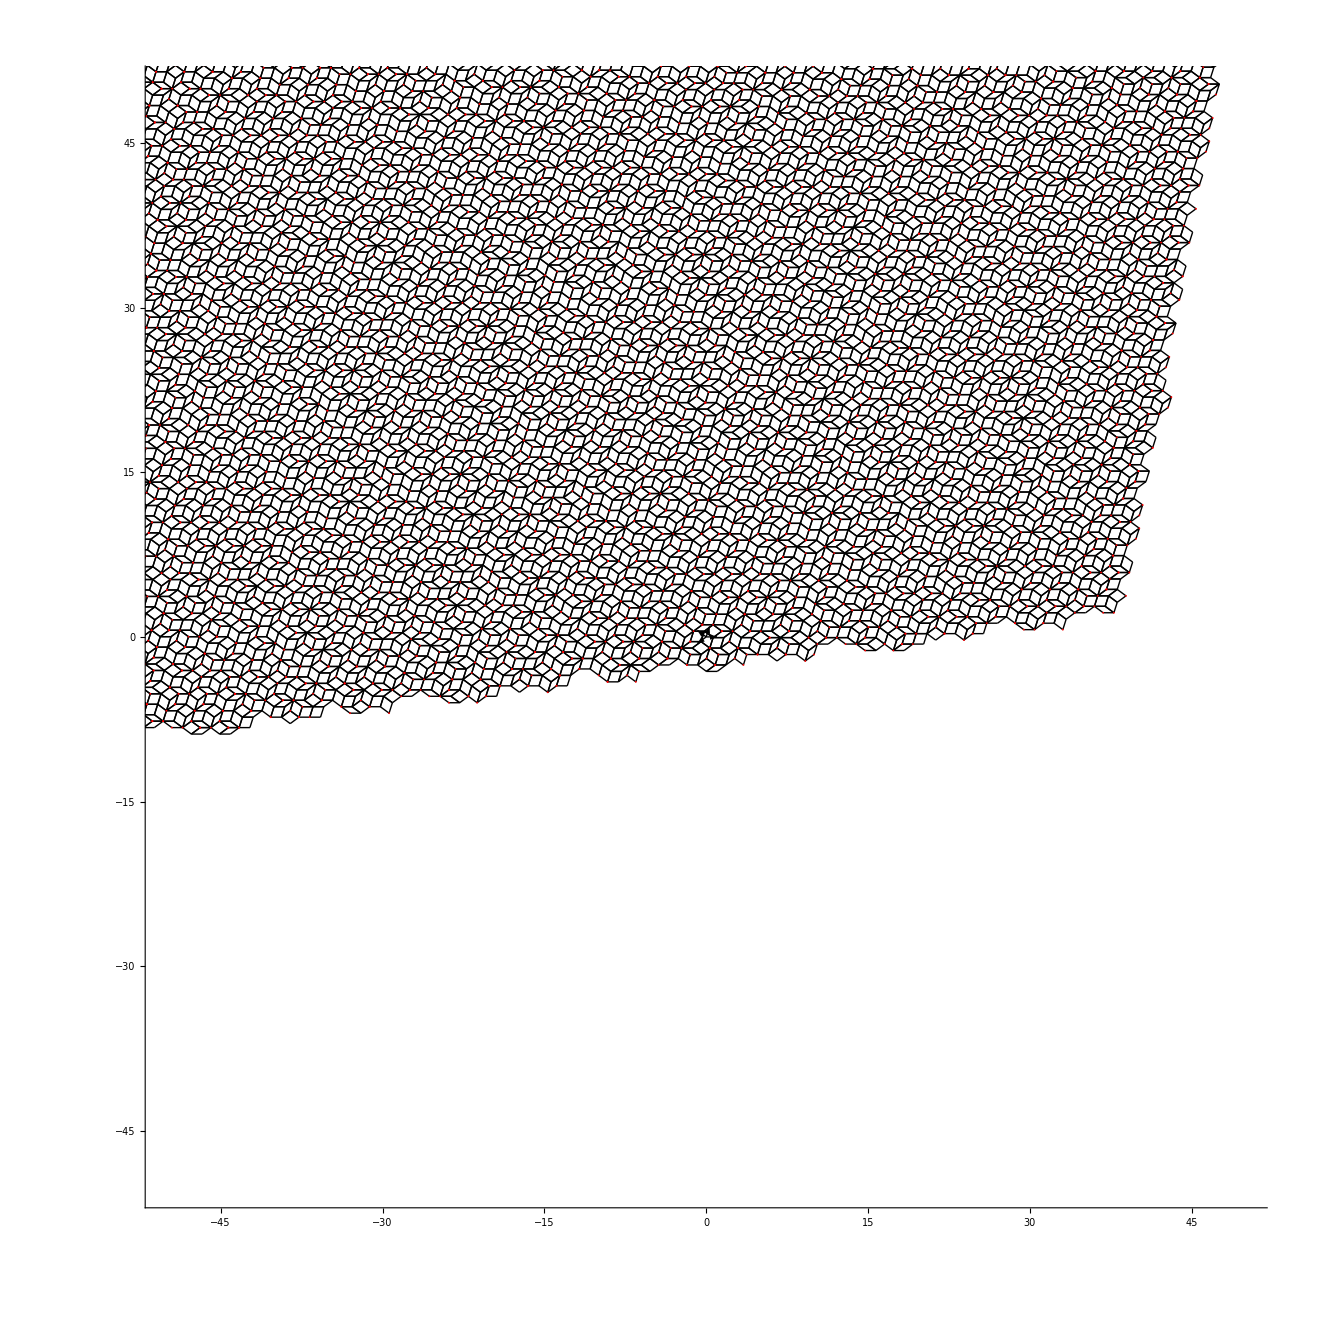

```mathematica
Show[basis,tiles[[All,2]],
Graphics[{PointSize[0.001],Red,Point[tiles[[All,1,{1,2}]]]}],
AspectRatio->1,PlotRange->{{-100,100},{-100,100}}]
```